## Bose Hubbard Distributions and Scaling

#### # of states in Na

```mathematica
ns[n_,L_]:=(((n+L/2-1)!)/(n!(L/2-1)!))
```

#### Normalized now by P(# of atoms in system size)

```mathematica
pn2[n_,L_]:=((((L-n)+L/2-1)!)/((L-n)!(L/2-1)!)) (((n+L/2-1)!)/(n!(L/2-1)!))/(((L+L-1)!)/(L!(L-1)!))
pnln[n_,l_,L_]:=((((L-n)+l-1)!)/((L-n)!(l-1)!)) (((n+(L-l)-1)!)/(n!((L-l)-1)!))/(((L+L-1)!)/(L!(L-1)!))
```

#### Testing Distributions(normalization)

```mathematica
TestMENormalize=N[Table[Sum[pn2[n,L],{n,0,L}],{L,2,40}]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Testing Distribution shape
```

Distribution shape Testing

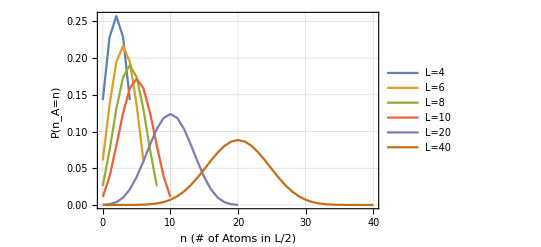

```mathematica
ListPlot[{Table[{n,pn2[n,4]},{n,0,4}],
Table[{n,pn2[n,6]},{n,0,6}],
Table[{n,pn2[n,8]},{n,0,8}],
Table[{n,pn2[n,10]},{n,0,10}],
Table[{n,pn2[n,20]},{n,0,20}],
Table[{n,pn2[n,40]},{n,0,40}]
},
PlotLegends-> {"L=4","L=6","L=8","L=10","L=20","L=40"},
Joined-> True,
Frame-> True,
GridLines-> Automatic,
FrameLabel-> {"n (# of Atoms in L/2)","P(n_A=n)","Bose Hubbard T=Infinity"}
]
```

```mathematica
Sum[pn2[ii,6],{ii,0,6}]
```

1

```mathematica
Sum[pnln[ii,4,8],{ii,0,8}]
```

1

## Calculating S_p from the P(n_A=n) when L_A=L/2

```mathematica
sp[L_]:=-Sum[pn2[n,L]Log[pn2[n,L]]
,
{n,0,L}
]
```

```mathematica
Scaling of Sp for system size L and sub system always L/2 (linear plot)
```

1/2 always and for L^2 linear of plot Scaling size Sp sub system^2

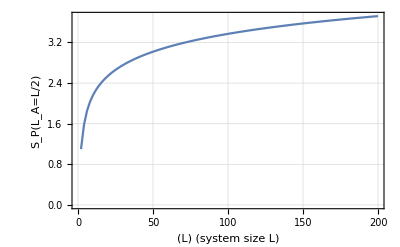

```mathematica
spvals=Table[{l,sp[l]},{l,2,200,2}];
ListPlot[{spvals},
Joined-> True,
Frame-> True,
FrameLabel-> {"(L) (system size L)","S_P(L_A=L/2)","Scaling of S_P"},
GridLines-> Automatic
]
```

```mathematica
Scaling of Sp for system size L and sub system always L/2 (log plot)
```

1/2 always and for L^2 log of plot Scaling size Sp sub system^2

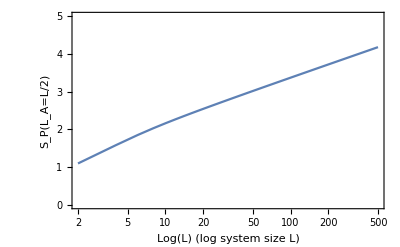

```mathematica
spvals=Table[{l,sp[l]},{l,2,500,2}];
ListLogLinearPlot[{spvals},
PlotRange->{ {2,500},{0,5}},
Joined-> True,
Frame-> True,
FrameLabel-> {"Log(L) (log system size L)","S_P(L_A=L/2)","Scaling of S_P"},
GridLines-> Automatic
]
```

## What about Fluctuations?

```mathematica
nf2[L_]:=Sum[pn2[n,L] n^2,{n,0,L}]-Sum[pn2[n,L]n,{n,0,L}]^2
```

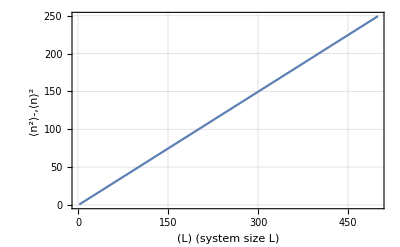

```mathematica
nfvals=Table[{l,nf2[l]},{l,2,500,2}];
ListPlot[{nfvals},
Joined-> True,
Frame-> True,
FrameLabel-> {"(L) (system size L)","⟨n^2⟩-,⟨n⟩^2","Scaling of Fluctuations"},
GridLines-> Automatic
]
```

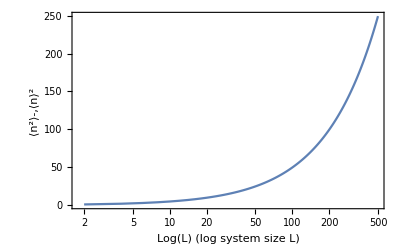

```mathematica
nfvals=Table[{l,nf2[l]},{l,2,500,2}];
ListLogLinearPlot[{nfvals},
Joined-> True,
Frame-> True,
FrameLabel-> {"Log(L) (log system size L)","⟨n^2⟩-,⟨n⟩^2","Scaling of Fluctuations"},
GridLines-> Automatic
]
```

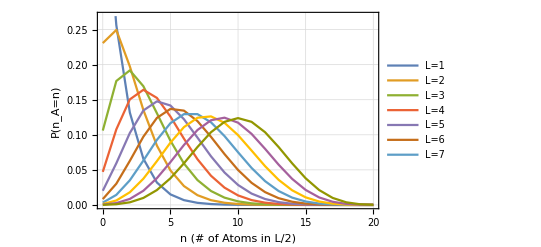

```mathematica
pnln[n_,l_,L_]:=((((L-n)+(L-l)-1)!)/((L-n)!((L-l)-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((L+L-1)!)/(L!(L-1)!))

ListPlot[{Table[{n,pnln[n,1,20]},{n,0,20}],
Table[{n,pnln[n,2,20]},{n,0,20}],
Table[{n,pnln[n,3,20]},{n,0,20}],
Table[{n,pnln[n,4,20]},{n,0,20}],
Table[{n,pnln[n,5,20]},{n,0,20}],
Table[{n,pnln[n,6,20]},{n,0,20}],
Table[{n,pnln[n,7,20]},{n,0,20}],
Table[{n,pnln[n,8,20]},{n,0,20}],
Table[{n,pnln[n,9,20]},{n,0,20}],
Table[{n,pnln[n,10,20]},{n,0,20}]
},
PlotLegends-> {"L=1","L=2","L=3","L=4","L=5","L=6","L=7"},
Joined-> True,
Frame-> True,
GridLines-> Automatic,
FrameLabel-> {"n (# of Atoms in L/2)","P(n_A=n)","Bose Hubbard T=Infinity"}
]
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

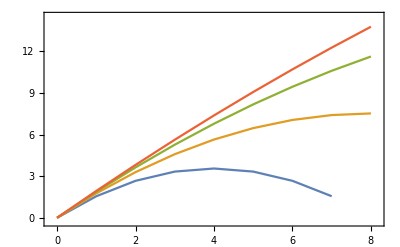

```mathematica
pn2[n_,L_]:=((((L-n)+L/2-1)!)/((L-n)!(L/2-1)!)) (((n+L/2-1)!)/(n!(L/2-1)!))/(((L+L-1)!)/(L!(L-1)!))
pnln[n_,l_,L_]:=((((L-n)+(L-l-1))!)/((L-n)!(L-l-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((L+L-1)!)/(L!(L-1)!))
pnF[l_,L_]:=Total[Table[pnln[n,l,L] n^2,{n,1,L}]]-Total[Table[pnln[n,l,L]n,{n,1,L}]]^2
ListPlot[{Table[{l,pnF[l,8]},{l,0,8}],
Table[{l,pnF[l,16]},{l,0,8}],
Table[{l,pnF[l,32]},{l,0,8}],
Table[{l,pnF[l,64]},{l,0,8}]}]
```

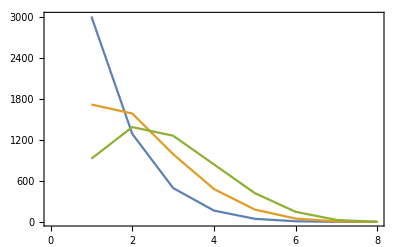

```mathematica
Ns[n_,l_,L_]:=((((L-n)+(L-l-1))!)/((L-n)!(L-l-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))
ListPlot[{Table[{l,Ns[0,l,8]},{l,1,8}],
Table[{l,Ns[1,l,8]},{l,1,8}],
Table[{l,Ns[2,l,8]},{l,1,8}]}]
```

```mathematica
FullSimplify[pnF[l,L]/L]
```

(2 l (-l+L))/(L (1+L))

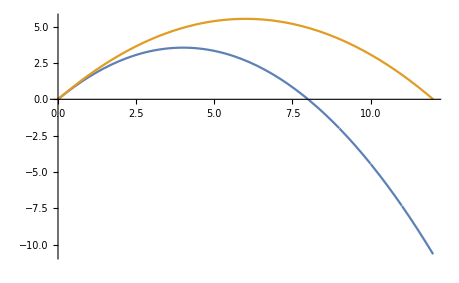

```mathematica
Plot[{pnF[l,8],pnF[l,12]},{l,0,12}]
```

```mathematica
pnlnN[n_,Nt_,l_,L_]:=((((Nt-n)+(L-l)-1)!)/((Nt-n)!((L-l)-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((Nt+L-1)!)/(Nt!(L-1)!))
pnFN[l_,L_,NS_,NE_]:=Sum[pnln[n,NE,l,L] n^2,{n,NS,NE}]-Sum[pnln[n,NE,l,L]n,{n,NS,NE}]^2
Plot[{pnFN[l,8,0,1],pnFN[l,8,0,8]},{l,0,8}]
```

-Graphics-

```mathematica
FullSimplify[pnFN[l,L,Nt]]
```

pnFN[l,L,Nt]

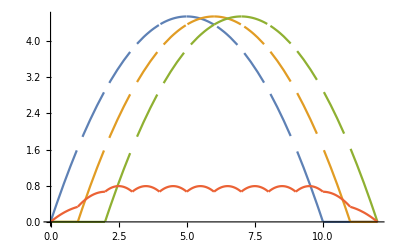

```mathematica
WNDWF[x_,L_]:=If[x>0,If[x<L,1,0],0];
LN=3;
Plot[{pnF[l,10] WNDWF[l,10],pnF[l-1,10] WNDWF[l-1,10],pnF[l-2,10] WNDWF[l-2,10],
Sum[pnF[l-n,LN] WNDWF[l-n,LN]/LN,{n,0,9}]},{l,0,12}]
```

```mathematica
a=0.1
Manipulate[
Plot[a(x-10)+(1-a)(Exp[-Abs[-x/l]]-Exp[-Abs[(20-x)/l]]),{x,0,20}],
{l,1,20}
]
```

0.1

```mathematica
Manipulate[
Plot[{Sinh[-x/b]/Sinh[1/b],-b Cosh[-x/b]/Sinh[1/b]+b Cosh[1/b]/Sinh[1/b]},{x,-1,1},
PlotRange-> {{-1,1},{-1,1}}],
{b,0.1,2}
]
```

```mathematica
Integrate[Sinh[-x/b],x]
```

-b Cosh[x/b]

```mathematica
Manipulate
```

Manipulate

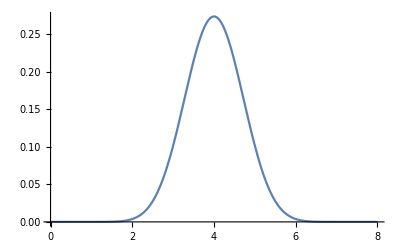

```mathematica
Plot[(8!/((8-x) !(x!)))((8-x)/8)^x(x/8)^(8-x),{x,0,8}]
```

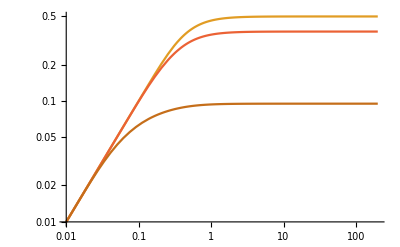

```mathematica
LogLogPlot[{Sinh[-0/b]/Sinh[1/b],-b Cosh[-0/b]/Sinh[1/b]+b Cosh[1/b]/Sinh[1/b],
Sinh[-0.5/b]/Sinh[1/b],-b Cosh[-0.5/b]/Sinh[1/b]+b Cosh[1/b]/Sinh[1/b],
Sinh[-0.9/b]/Sinh[1/b],-b Cosh[-0.9/b]/Sinh[1/b]+b Cosh[1/b]/Sinh[1/b]},{b,0.01,200}]
```

## Hilbert Space Size

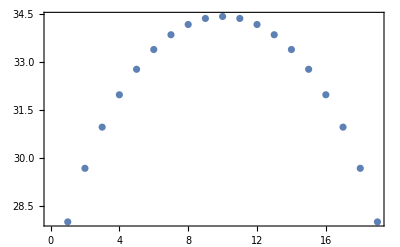

```mathematica
NL[n_,l_,L_]:=((((L-n)+l-1)!)/((L-n)!(l-1)!)) 
NR[n_,l_,L_]:=(((n+(L-l)-1)!)/(n!((L-l)-1)!))
NLR[l_,NT_]:=Sum[NL[ii,l,NT],{ii,0,NT}] Sum[NR[ii,l,NT],{ii,0,NT}];

NLP=20;
ListPlot[
{
Table[{l, Log[NLR[l,NLP]]},{l,1,NLP-1}]
},
Joined-> False
]
```

```mathematica
pnlnN[n_,Nt_,l_,L_]:=((((Nt-n)+(L-l)-1)!)/((Nt-n)!((L-l)-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((Nt+L-1)!)/(Nt!(L-1)!))
pnFN[l_,L_,NE_]:=Sum[pnlnN[n,NE,l,L] n^2,{n,0,NE}]-Sum[pnlnN[n,NE,l,L]n,{n,0,NE}]^2
FullSimplify[pnFN[l,L,n]]
```

(Gamma[L] (1/(3+l-L)(1+l-L) (2+l-L) L! (L+n)! ((L+n) ((-1+L) (-1+l+L)+(-1-l+L) (-3+2 L) n+(1+l-L) (2+l-L) n^2) L! (l+n)!-(-1+L) L (-1+l+L) l! (L+n)!) Gamma[l]-((L+n) (-1+L+(-1-l+L) n) L! (l+n)!-(-1+L) L l! (L+n)!)^2 Gamma[L]))/((1+l-L)^2 (2+l-L)^2 Gamma[l]^2 Gamma[1+L]^2 Gamma[1+L+n]^2)

```mathematica
FullSimplify[pnFN[l,L,1]]
FullSimplify[pnFN[l,L,2]]
FullSimplify[pnFN[l,L,3]]
FullSimplify[pnFN[l,L,4]]
FullSimplify[pnFN[l,L,5]]
FullSimplify[pnFN[l,L,10]]
```

(l (-l+L))/L^2

(2 l (2+L) (-l+L))/(L^2 (1+L))

-(3 l (l-L) (3+L))/(L^2 (1+L))

-(4 l (l-L) (4+L))/(L^2 (1+L))

-(5 l (l-L) (5+L))/(L^2 (1+L))

-(10 l (l-L) (10+L))/(L^2 (1+L))

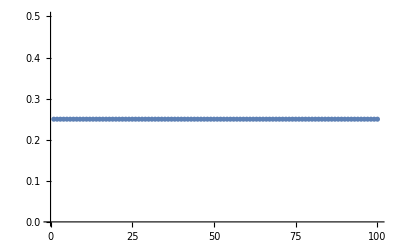

```mathematica
ListPlot[
Table[{x,pnFN[5,10,1]},{x,1,100}]
]
```

```mathematica
Manipulate[
Plot[-Sinh[ξ/x]/Sinh[1/ξ]/ Abs[2 x]!,{x,-1,1}],
{ξ,0.1,1}
]
```

```mathematica
pnln[n_,l_,L_]:=((((L-n)+(L-l-1))!)/((L-n)!(L-l-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((L+L-1)!)/(L!(L-1)!))
pnF[l_,L_,ν_]:=Total[Table[pnln[n,l,L] n^2,{n,1,ν L}]]-Total[Table[pnln[n,l,L]n,{n,1,ν L}]]^2
```

```mathematica
FullSimplify[pnF[l,L,1]]/L
```

(l Gamma[1+L] Gamma[-1-l+2 L] (Gamma[2 L] Gamma[-l+L]-l Gamma[1+L] Gamma[-1-l+2 L]))/(L Gamma[2 L]^2 Gamma[-l+L]^2)

```mathematica
pnlnN[n_,Nt_,l_,L_]:=((((Nt-n)+(L-l)-1)!)/((Nt-n)!((L-l)-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((Nt+L-1)!)/(Nt!(L-1)!))
pnFN[l_,L_,NE_]:=Sum[pnlnN[n,NE,l,L] n^2,{n,0,NE}]-Sum[pnlnN[n,NE,l,L]n,{n,0,NE}]^2
FullSimplify[pnFN[l,L,n]]
```

(Gamma[L] (1/(3+l-L)(1+l-L) (2+l-L) L! (L+n)! ((L+n) ((-1+L) (-1+l+L)+(-1-l+L) (-3+2 L) n+(1+l-L) (2+l-L) n^2) L! (l+n)!-(-1+L) L (-1+l+L) l! (L+n)!) Gamma[l]-((L+n) (-1+L+(-1-l+L) n) L! (l+n)!-(-1+L) L l! (L+n)!)^2 Gamma[L]))/((1+l-L)^2 (2+l-L)^2 Gamma[l]^2 Gamma[1+L]^2 Gamma[1+L+n]^2)